```mathematica
Clear["Global`*"];

(* Exploitation parameter *)
beta = {beta1,beta2}; 
(* Learning rate *)
alpha = {alpha1,alpha2};
(* Discount factor *)
gamma = {gamma1,gamma2};

(* State transition matrix *)
(* t_s,a1,a2,s' *)
T = {{{{t1111,t1112},{t1121,t1122}},{{t1211,t1212},{t1221,t1222}}},{{{t2111,t2112},{t2121,t2122}},{{t2211,t2212},{t2221,t2222}}}}; 

(* Reward matrix *)
(* r_i,s,a1,a2 *)
RM = {{{{r1111,r1112},{r1121,r1122}},{{r1211,r1212},{r1221,r1222}}},{{{r2111,r2112},{r2121,r2122}},{{r2211,r2212},{r2221,r2222}}}};

(* Q-table *)
(* q_i,s,a *)
Q = {{{q111,q112},{q121,q122}},{{q211,q212},{q221,q222}}};

(* Behavior profiles as functions of Q *)
(* x_i,s,a *)
Z=Total[Exp[beta*Q],{3}];
XQ = Exp[beta*Q]/Z;

(* Behavior profiles as independent variables *)
(* x_i,s,a *)
X = {{{X111,X112},{X121,X122}},{{X211,X212},{X221,X222}}};

(* Q as functions of X *)
QX = Log[X]/beta ;
(*QX = QX + Log[Z]*)
QXrule=Thread[Flatten[Q] -> Flatten[QX]];

(* Joint behavioral profile *)
(* Xvec_s,a1,a2 *)
Xs1 = Times @@{{{X111,X111},{X112,X112}},{{X211,X212},{X211,X212}}}; (* s=1,a1,a2 *)
Xs2 = Times @@{{{X121,X121},{X122,X122}},{{X221,X222},{X221,X222}}}; (* s=2,a1,a2 *)
Xwhole={Xs1,Xs2};
```

```mathematica
(* Deterministic limit (Eq. 17) ------------------------------------------------------------*)

Clear[alpha1,alpha2,beta1,beta2,gamma1,gamma2];
(* s',a'<R>_i,s,a *)
Risa =ConstantArray[0,{2,2,2}];
(* i's = indices, j's = summation *)
For[i1=1,i1<3,i1++, (*i*)
For[i2=1,i2<3,i2++,(*s*)
For[i3=1,i3<3,i3++,(*a*)
For[j1=1,j1<3,j1++,(*s'*)
For[j2=1,j2<3,j2++,(*a'*)
(* Other agent's id *)
If[i1==1,iother=2;a1=i3;a2=j2;,iother=1;a1=j2;a2=i3;];
Risa[[i1,i2,i3]] +=XQ[[iother,i2,j2]]*T[[i1,a1,a2,j1]]*RM[[i1,i2,a1,a2]];
]]]]];

(* s',a'<maxQ>_i,s,a *)
maxQisa = ConstantArray[0,{2,2,2}];
(* i's = indices, j's = summation *)
For[i1=1,i1<3,i1++, (*i*)
For[i2=1,i2<3,i2++,(*s*)
For[i3=1,i3<3,i3++,(*a*)
For[j1=1,j1<3,j1++,(*s'*)
For[j2=1,j2<3,j2++,(*a'*)
(* Other agent's id *)
If[i1==1,iother=2;a1=i3;a2=j2;,iother=1;a1=j2;a2=i3;];
maxQisa[[i1,i2,i3]] +=XQ[[iother,i2,j2]]*T[[i1,a1,a2,j1]]*Max[Q[[i1,j1]]];
]]]]];

(* TD_i,s,a (Eq. 17 in terms of q) *)
TD=(1-gamma) * Risa + gamma*maxQisa-Q;

(* State 1 only *)
(* Variable change q -> X *)
RuleProb = {X112 -> 1-X111,X122->1-X121,X212->1-X211,X222->1-X221}; (* Normalization *)
TD111X = TD[[1,1,1]] /. QXrule/.RuleProb;
TD112X = TD[[1,1,2]] /. QXrule/.RuleProb;
TD211X = TD[[2,1,1]] /. QXrule/.RuleProb;
TD212X = TD[[2,1,2]] /. QXrule/.RuleProb;

(* Average over state 2 parameters *)
$Assumptions = beta1>0&&beta2>0;
TD111Xavg = Integrate[TD111X,{X121,0,1}];
TD112Xavg = Integrate[TD112X,{X121,0,1}];
TD211Xavg = Integrate[TD211X,{X221,0,1}];
TD212Xavg = Integrate[TD212X,{X221,0,1}];
$Assumptions = True;

(* Get rid of piecewise (messes up with VectorPlot) *)
If[Depth[TD111Xavg]>5,
TD111Xavg=TD111Xavg[[1,1,1]]*Boole[TD111Xavg[[1,1,2]]] +TD111Xavg[[2]]*Boole[!TD111Xavg[[1,1,2]]];,
]
If[Depth[TD112Xavg]>5,
TD112Xavg=TD112Xavg[[1,1,1]]*Boole[TD112Xavg[[1,1,2]]] +TD112Xavg[[2]]*Boole[!TD112Xavg[[1,1,2]]];,
]
If[Depth[TD211Xavg]>5,
TD211Xavg=TD211Xavg[[1,1,1]]*Boole[TD211Xavg[[1,1,2]]] +TD211Xavg[[2]]*Boole[!TD211Xavg[[1,1,2]]];,
]
If[Depth[TD212Xavg]>5,
TD212Xavg=TD212Xavg[[1,1,1]]*Boole[TD212Xavg[[1,1,2]]] +TD212Xavg[[2]]*Boole[!TD212Xavg[[1,1,2]]];,
]
```

```mathematica
(* X evolution equation (Eq. 11) ------------------------------------------------------------*)
X111next=X111*Exp[alpha1*beta1*TD111Xavg]/(X111*Exp[alpha1*beta1*TD111Xavg]+(1-X111)*Exp[alpha1*beta1*TD112Xavg]);
X211next=X211*Exp[alpha2*beta2*TD211Xavg]/(X211*Exp[alpha2*beta2*TD211Xavg]+(1-X211)*Exp[alpha2*beta2*TD212Xavg]);
```

```mathematica
(* Two-state penny matching game ------------------------------------------------------------------------------------*)

(* State 1: Agent 1 jumps left -> transition to state 2 *)
(* t_s,a1,a2,s' *)
t1111 = 0;t1112 = 1;t1121=0;t1122=1;  (* Agent 1 jumps left *)
t1211 = 1;t1212 = 0;t1221=1;t1222=0; (* Agent 1 jumps right *)
(* State 2: Agent 1 kicks right -> transition to state 1 *)
t2111 = 0;t2112 = 1;t2121=0;t2122=1; (* Agent 1 kicks left *)
t2211 = 1;t2212 = 0;t2221=1;t2222=0; (* Agent 1 kicks right *)

(* r_i,s,a1,a2 *)
r1111=1;r1112=0;r1121=0;r1122=1; (* Agent 1 is keeper in state 1 *)
r1211=0;r1212=1;r1221=1;r1222=0; (* Agent 1 is kicker in state 2 *)
r2111=0;r2112=1;r2121=1;r2122=0; (* Agent 2 is kicker in state 1 *)
r2211=1;r2212=0;r2221=0;r2222=1; (* Agent 2 is keeper in state 2 *)
```

```mathematica
(* Two-state IPD ------------------------------------------------------------------------------------*)

(* a: 1 = coop., 2 = defect *)
(* Higher prob. (0.9) of switching state if one defects and the other doesn't (i.e. action mismatch) *)

(* State 1 *)
(* t_s,a1,a2,s' *)
t1111 = 0.9;t1112 = 0.1;t1121=0.1;t1122=0.9; 
t1211 = 0.1;t1212 = 0.9;t1221=0.9;t1222=0.1;
(* State 2 *)
t2111 = 0.1;t2112 = 0.9;t2121=0.9;t2122=0.1;
t2211 = 0.9;t2212 = 0.1;t2221=0.1;t2222=0.9;

(* r_i,s,a1,a2 *)
r1111=3;r1112=0;r1121=10;r1122=2; 
r1211=4;r1212=0;r1221=10;r1222=1;
r2111=3;r2112=10;r2121=0;r2122=2;
r2211=4;r2212=10;r2221=0;r2222=1;
```

```mathematica
(* Set hyperparameters ---------------------------------------------------------------------*)
Params = {alpha1->0.9440917194382215,alpha2->0.03433809858193104,beta1->3.9328841338044835,beta2->17.57331125765527,gamma1->0.8512793689118644,gamma2->0.3838445359254459};


Params = {alpha1->0.8,alpha2->0.8,beta1->5.0,beta2->5.0,gamma1->0.1,gamma2->0.1};
Params = {alpha1->0.02,alpha2->0.02,beta1->5.0,beta2->5.0,gamma1->0.9,gamma2->0.1};
```

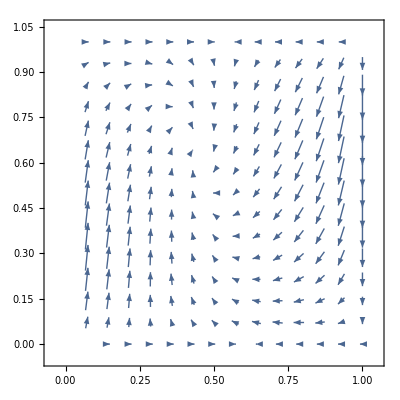

```mathematica
(* Plot -----------------------------------------------------------------------------------*)
(* Observations: the agent with greater alpha seems to be setting the dynamics (changing the other agent's parameters don't change anything) *)
(* Setting smaller gamma seems to be better *)
VectorPlot[{X111next-X111/.Params,X211next-X211/.Params},{X111,0,1},{X211,0,1}]
```

```mathematica
(* Appendix A Alternative -------------------------------------------------------------------*)
 TDRules = TD /. QXrule/.RuleProb; (* i,s,a *)
Aisa=X * Exp[alpha * beta * TDRules];
Simplify[Aisa[[1,1,1]]]
```

ⅇ^(alpha1 beta1 ((1-gamma1) (-r1112 (t1121+t1122) (-1+X211)+r1111 (t1111+t1112) X211)-Log[X111]/beta1+gamma1 ((t1121+t1111 X211-t1121 X211) Max[Log[1-X111]/beta1,Log[X111]/beta1]+(t1122+t1112 X211-t1122 X211) Max[Log[1-X121]/beta1,Log[X121]/beta1]))) X111

```mathematica
(* Numerical Simulation ---------------------------------------------------------------------*)TimeSteps = 1000; (* Number of time steps *)

(* Initial conditions *)
Qvals = {{{0,0.916},{0.829,1}},{{0.916,0},{0.921,1}}};

(* Agent parameters *)
alpha1 = 0.8;
alpha2 = 0.8;
beta1 = 8.0;
beta2 = 8.0;
gamma1 = 0.1;
gamma2 = 0.1;

(* Record probabilities *)
X111List={};(* Agent 1, state 1 *)
X211List={};(* Agent 2, state 1 *)
X121List={};(* Agent 1, state 2 *)
X221List={};(* Agent 2, state 2 *)

For[t=0, t<TimeSteps, t++,
	
	Qvals = Qvals + alpha*TD /.Thread[Flatten[Q]->Flatten[Qvals]];
	X111List = Append[X111List,XQ[[1,1,1]] /.Thread[Flatten[Q]->Flatten[Qvals]] ];
	X211List = Append[X211List,XQ[[2,1,1]] /.Thread[Flatten[Q]->Flatten[Qvals]] ];
	X121List = Append[X121List,XQ[[1,2,1]] /.Thread[Flatten[Q]->Flatten[Qvals]] ];
	X221List = Append[X221List,XQ[[2,2,1]] /.Thread[Flatten[Q]->Flatten[Qvals]] ];
]
```

```mathematica
(* Appendix A -----------------------------------------------------------------------------*)

(* Series expression from probability condition *)
Xseries = 1 +2*X-Total[X,{3}];
Xserieswhole = Times @@ Xseries;

(* A6 (derivative) ------------------------------------------*)
(* dX_i,s,a / dX_j,r,b *)
A6 = D[Xseries,{X,1}];

(* A15 ---------------------------------------------------- *)
(* dX_vec_s,a1,a2 / dX_j,r,b *) (* Action pair differentiation *)
dXdX = ConstantArray[0,{2,2,2,2,2,2}];
For[i1=1,i1<3,i1++, (*s*)
For[i2=1,i2<3,i2++,(*a1*)
For[i3=1,i3<3,i3++,(*a2*)
For[i4=1,i4<3,i4++,(*j*) (* Agent being differentiated *)
For[i5=1,i5<3,i5++,(*r*)
For[i6=1,i6<3,i6++,(*b*)
If[i4==1,iother=2;aother=i3;adiff=i2;,iother=1;aother=i2;adiff=i3;]; (* Get the differentiated agent's action and other guy's index and action *)
dXdX[[i1,i2,i3,i4,i5,i6]] += X[[iother,i1,aother]]*A6[[i4,i1,adiff,i4,i5,i6]];
]]]]]];

(* d_s',a1,a2<R>_i,s / dX_j,r,b *)
A15 = ConstantArray[0,{2,2,2,2,2}]; (* Initialize *)
(* i's = indices, j's = summation *)
For[i1=1,i1<3,i1++, (*i*)
For[i2=1,i2<3,i2++,(*s*)
For[i3=1,i3<3,i3++,(*j*)
For[i4=1,i4<3,i4++,(*r*)
For[i5=1,i5<3,i5++,(*b*)
For[j1=1,j1<3,j1++,(*s'*)
For[j2=1,j2<3,j2++,(*a1*)
For[j3=1,j3<3,j3++,(*a2*)
A15[[i1,i2,i3,i4,i5]] +=dXdX[[i2,j2,j3,i3,i4,i5]]*T[[i2,j2,j3,j1]]*RM[[i1,i2,j2,j3]];
]]]]]]]];

(* A14 ---------------------------------------------------- *)
(* d_a1,a2<T>_s,s' / dX_j,r,b *) (* A12 where a is not fixed *)
A12unfix = ConstantArray[0,{2,2,2,2,2,2}];
(* i's = indices, j's = summation *)
For[i1=1,i1<3,i1++, (*s*)
For[i2=1,i2<3,i2++,(*s'*)
For[i3=1,i3<3,i3++,(*j*)
For[i4=1,i4<3,i4++,(*r*)
For[i5=1,i5<3,i5++,(*b*)
For[j1=1,j1<3,j1++,(*a1*)
For[j2=1,j2<3,j2++,(*a2*)
A12unfix[[i1,i2,i3,i4,i5]] +=dXdX[[i1,j1,j2,i3,i4,i5]]*T[[i1,j1,j2,i2]];
]]]]]]];

(* dM_i,s,s' / dX_j,r,b *)
A14 = ConstantArray[0,{2,2,2,2,2,2}];
For[i1=1,i1<3,i1++, (*i*)
For[i2=1,i2<3,i2++,(*s*)
For[i3=1,i3<3,i3++,(*s'*)
For[i4=1,i4<3,i4++,(*j*)
For[i5=1,i5<3,i5++,(*r*)
For[i6=1,i6<3,i6++,(*b*)
A14[[i1,i2,i3,i4,i5,i6]] = -gamma[[i1]] * A12unfix[[i2,i3,i4,i5,i6]];
]]]]]];



(* A14 ---------------------------------------------------- *)
```